51 a-2 x+68 a x+a x^4

-2/3+(3776 a)/45

15/1888

(15 (-1+x)^2 (3+2 x+x^2))/1888

x+(15 (-1+x)^2 (3+2 x+x^2))/1888

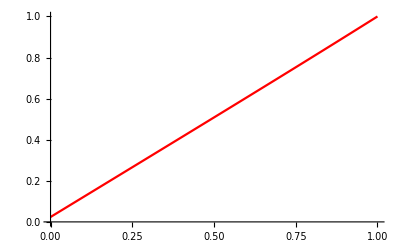

```mathematica
l=b=1;
k=3;
ϕ[x_]=(x-l)^2 (3l^2+2l x+x^2);
v[x_]=a ϕ[x];
u[x_]=v[x]+x;
eq[x_]=b u[x]-k x+(2l+x)D[u[x], {x,4}]+2D[u[x], {x,3}]//Expand
sol=Integrate[eq[x] ϕ[x], {x,0,l}]
na=Solve[sol==0,a][[1,1,2]]
nv[x_]=na ϕ[x]
nu[x_]=nv[x]+x

Plot[{nu[x]},{x,0,l},PlotStyle->{{Red}}]
```